```mathematica
<<RLBot`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = ImportNDJSON["log.ndjson", {2}];
```

```mathematica
cars = #["car"] & /@ data;
inputs = #["inputs"] & /@ data;
times = #["time"] & /@ data;
follows = #["follow"] & /@ data;
```

```mathematica
splan = #["expected_s"] & /@ data;
sactual = #["s"] & /@ data;
xplan = (List @@#["expected_position"] & /@ data[[2;;-1]]) /.{"KeyAbsent","expected_position"}->Nothing;
xactual =  #["car"]["x"] & /@ data;
vplan = (List @@ {#["time"], #["expected_speed"]} & /@ data[[2;;-1]]) /. {"KeyAbsent","expected_speed"}->1
vactual =  {#["time"],Norm[#["car"]["v"]]} & /@ data;
```

{{305.978,1004.84},{305.986,1007.52},{305.994,1010.21},{306.01,1015.05},3837,{338.082,1002.46},{338.09,1001.74},{338.099,1001.01},{338.107,1000.27}}
 |  |  |  |

```mathematica
serror = #["expected_s"]-#["s"] & /@ data;
```

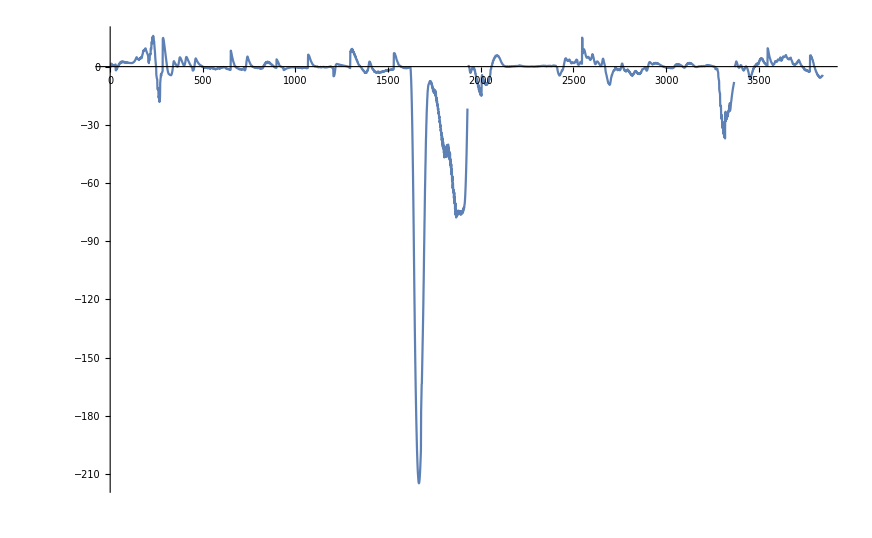

```mathematica
ListLinePlot[serror, PlotRange->All]
```

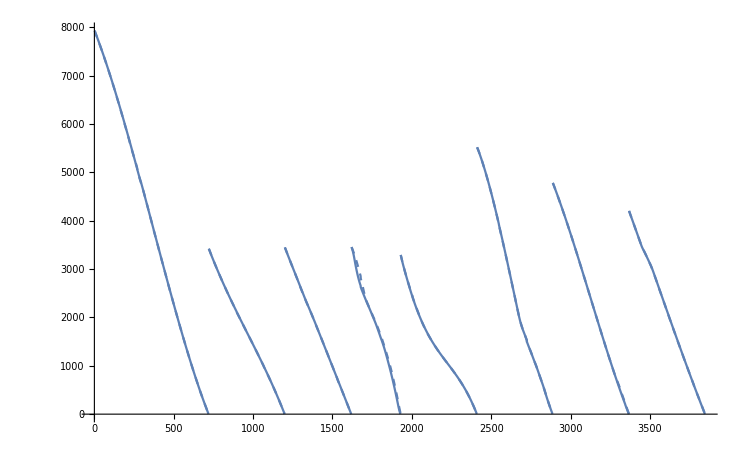

```mathematica
Show[
ListLinePlot[splan],
ListLinePlot[sactual, PlotStyle->Dashed]
]
```

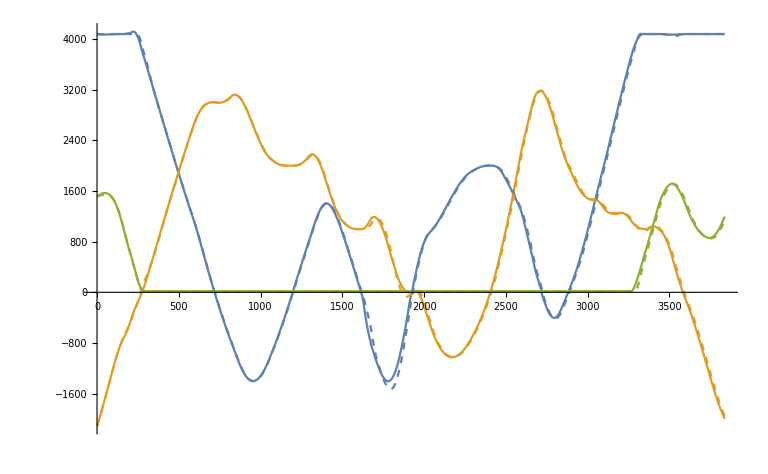

```mathematica
Show[
ListLinePlot[Transpose[xplan]],
ListLinePlot[Transpose[xactual], PlotStyle->Dashed]
]
```

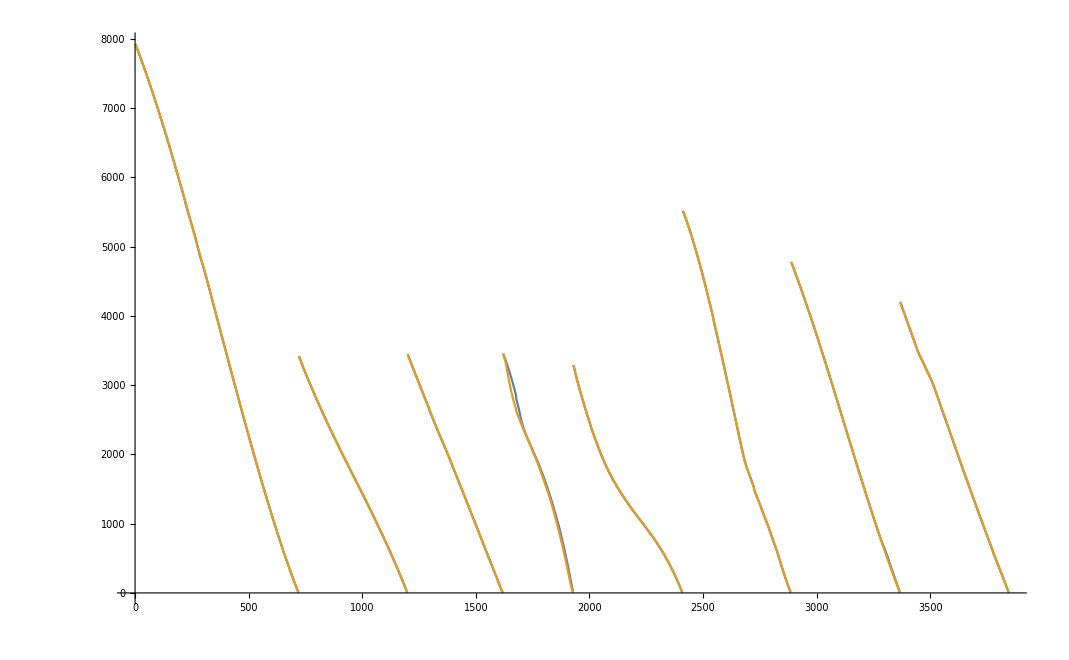

```mathematica
ListLinePlot[{sactual,splan}]
```

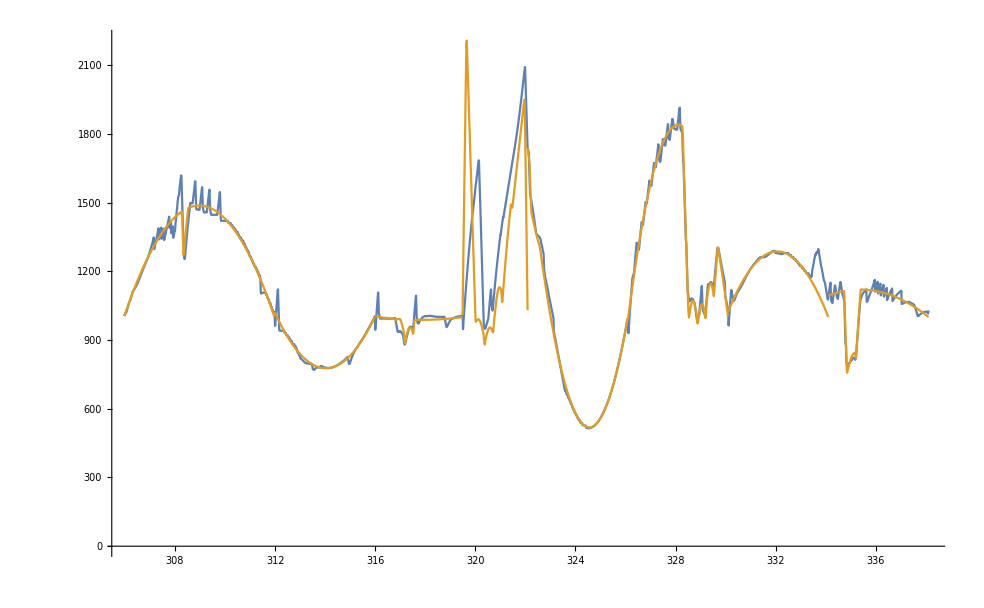

```mathematica
ListLinePlot[{vactual, vplan}]
```

```mathematica
Graphics3D[
Line[xactual]
]
```

-Graphics3D-

```mathematica
vplan
```

{{305.978,1004.84},{305.986,1007.52},{305.994,1010.21},{306.01,1015.05},3837,{338.082,1002.46},{338.09,1001.74},{338.099,1001.01},{338.107,1000.27}}
 |  |  |  |

```mathematica
Graphics3D[{
Red,
Line[xactual],
Blue,
Line[xplan],
Black,
Point /@ xactual[[ids]]
}]
```

-Graphics3D-

```mathematica
ids = Flatten[Position[Abs[#["steer"]] & /@ inputs, 1.0]]
```

{719,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,212,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2409,2756,2757,2758,2759,2760,2761,2762,2884,2885,2886,3367,3844,3845,3846}
 |  |  |  |